```mathematica
dmks2pi0funct[m_,ep_]:=498/Sqrt[(m/2)^2-498^2](InterpolatingFunction[…][m/(2*498)*ep*(1+Sqrt[1-(2*498/m)^2])]-InterpolatingFunction[…][m/(2*498)*ep*(1-Sqrt[1-(2*498/m)^2])])
```

```mathematica
dmkl3pi0funct[m_,ep_]:=498/Sqrt[(m/2)^2-498^2]*(InterpolatingFunction[…][m/(2*498)*ep*(1+Sqrt[1-(2*498/m)^2])]-InterpolatingFunction[…][m/(2*498)*ep*(1-Sqrt[1-(2*498/m)^2])])
```

```mathematica
dmklpipm0funct[m_,ep_]:=498/Sqrt[(m/2)^2-498^2]*(InterpolatingFunction[…][m/(2*498)*ep*(1+Sqrt[1-(2*498/m)^2])]-InterpolatingFunction[…][m/(2*498)*ep*(1-Sqrt[1-(2*498/m)^2])])
```

```mathematica
normfunc[dmm_,f_,ep_]:=NIntegrate[(f),{ep,0,dmm}]
```

```mathematica
dmks2pi0norma[dmm_,ep_]:=((4*0.307)/Quiet[normfunc[dmm,dmks2pi0funct[dmm,ep],ep]]*dmks2pi0funct[dmm,ep])
```

```mathematica
dmkl3pi0norma[dmm_,ep_]:=((0.195*6)/Quiet[normfunc[dmm,dmkl3pi0funct[dmm,ep],ep]]*dmkl3pi0funct[dmm,ep])
```

```mathematica
dmklpipm0norma[dmm_,ep_]:=((0.125*2)/Quiet[normfunc[dmm,dmklpipm0funct[dmm,ep],ep]]*dmklpipm0funct[dmm,ep])
```

```mathematica
kshortlong[m_,emax_]:=Quiet[Plot[{Evaluate[dmks2pi0norma[m,ep]],Evaluate[dmkl3pi0norma[m,ep]],Evaluate[dmklpipm0norma[m,ep]],Evaluate[dmks2pi0norma[m,ep]+dmkl3pi0norma[m,ep]+dmklpipm0norma[m,ep]]},{ep,0,emax},PlotRange->Full,PlotStyle->  {Red,Blue,Green,Black},PlotLegends->{"Ks -> 2π0","Kl -> 3π0","Kl -> π+π-π0","Total Ks Kl"},PlotLabel->m "MeV Dark Matter -> Ks Kl Photon Spectrum" ]]
DM=1100
kfile[m_,ep_] :=
Evaluate[dmks2pi0norma[DM,ep]+
dmkl3pi0norma[DM,ep]+
dmklpipm0norma[DM,ep]]

elist=Quiet[N@Subdivide[0.01,1000,2000]]
dataset={elist,kfile[DM, elist]}
SetDirectory@NotebookDirectory[]
Export["Kls PDFs\s"<>ToString[DM]<>".csv",dataset, "CSV"]
```

1100

{0.01,0.509995,1.00999,1.50999,2.00998,2.50998,3.00997,3.50997,4.00996,4.50996,5.00995,5.50995,6.00994,6.50994,7.00993,7.50993,8.00992,8.50992,9.00991,9.50991,10.0099,10.5099,11.0099,11.5099,12.0099,12.5099,13.0099,13.5099,14.0099,14.5099,15.0099,15.5098,16.0098,16.5098,17.0098,17.5098,18.0098,18.5098,19.0098,19.5098,20.0098,20.5098,21.0098,21.5098,22.0098,22.5098,23.0098,23.5098,24.0098,24.5098,25.0098,25.5097,26.0097,26.5097,27.0097,27.5097,28.0097,28.5097,29.0097,29.5097,30.0097,30.5097,31.0097,31.5097,32.0097,32.5097,33.0097,33.5097,34.0097,34.5097,35.0097,35.5096,36.0096,36.5096,37.0096,37.5096,38.0096,38.5096,39.0096,39.5096,40.0096,40.5096,41.0096,41.5096,42.0096,42.5096,43.0096,43.5096,44.0096,44.5096,45.0096,45.5095,46.0095,46.5095,47.0095,47.5095,48.0095,48.5095,49.0095,49.5095,50.0095,50.5095,51.0095,51.5095,52.0095,52.5095,53.0095,53.5095,54.0095,54.5095,55.0095,55.5094,56.0094,56.5094,57.0094,57.5094,58.0094,58.5094,59.0094,59.5094,60.0094,60.5094,61.0094,61.5094,62.0094,62.5094,63.0094,63.5094,64.0094,64.5094,65.0094,65.5093,66.0093,66.5093,67.0093,67.5093,68.0093,68.5093,69.0093,69.5093,70.0093,70.5093,71.0093,71.5093,72.0093,72.5093,73.0093,73.5093,74.0093,74.5093,75.0093,75.5092,76.0092,76.5092,77.0092,77.5092,78.0092,78.5092,79.0092,79.5092,80.0092,80.5092,81.0092,81.5092,82.0092,82.5092,83.0092,83.5092,84.0092,84.5092,85.0092,85.5091,86.0091,86.5091,87.0091,87.5091,88.0091,88.5091,89.0091,89.5091,90.0091,90.5091,91.0091,91.5091,92.0091,92.5091,93.0091,93.5091,94.0091,94.5091,95.0091,95.509,96.009,96.509,97.009,97.509,98.009,98.509,99.009,99.509,100.009,100.509,101.009,101.509,102.009,102.509,103.009,103.509,104.009,104.509,105.009,105.509,106.009,106.509,107.009,107.509,108.009,108.509,109.009,109.509,110.009,110.509,111.009,111.509,112.009,112.509,113.009,113.509,114.009,114.509,115.009,115.509,116.009,116.509,117.009,117.509,118.009,118.509,119.009,119.509,120.009,120.509,121.009,121.509,122.009,122.509,123.009,123.509,124.009,124.509,125.009,125.509,126.009,126.509,127.009,127.509,128.009,128.509,129.009,129.509,130.009,130.509,131.009,131.509,132.009,132.509,133.009,133.509,134.009,134.509,135.009,135.509,136.009,136.509,137.009,137.509,138.009,138.509,139.009,139.509,140.009,140.509,141.009,141.509,142.009,142.509,143.009,143.509,144.009,144.509,145.009,145.509,146.009,146.509,147.009,147.509,148.009,148.509,149.009,149.509,150.009,150.508,151.008,151.508,152.008,152.508,153.008,153.508,154.008,154.508,155.008,155.508,156.008,156.508,157.008,157.508,158.008,158.508,159.008,159.508,160.008,160.508,161.008,161.508,162.008,162.508,163.008,163.508,164.008,164.508,165.008,165.508,166.008,166.508,167.008,167.508,168.008,168.508,169.008,169.508,170.008,170.508,171.008,171.508,172.008,172.508,173.008,173.508,174.008,174.508,175.008,175.508,176.008,176.508,177.008,177.508,178.008,178.508,179.008,179.508,180.008,180.508,181.008,181.508,182.008,182.508,183.008,183.508,184.008,184.508,185.008,185.508,186.008,186.508,187.008,187.508,188.008,188.508,189.008,189.508,190.008,190.508,191.008,191.508,192.008,192.508,193.008,193.508,194.008,194.508,195.008,195.508,196.008,196.508,197.008,197.508,198.008,198.508,199.008,199.508,200.008,200.508,201.008,201.508,202.008,202.508,203.008,203.508,204.008,204.508,205.008,205.508,206.008,206.508,207.008,207.508,208.008,208.508,209.008,209.508,210.008,210.508,211.008,211.508,212.008,212.508,213.008,213.508,214.008,214.508,215.008,215.508,216.008,216.508,217.008,217.508,218.008,218.508,219.008,219.508,220.008,220.508,221.008,221.508,222.008,222.508,223.008,223.508,224.008,224.508,225.008,225.508,226.008,226.508,227.008,227.508,228.008,228.508,229.008,229.508,230.008,230.508,231.008,231.508,232.008,232.508,233.008,233.508,234.008,234.508,235.008,235.508,236.008,236.508,237.008,237.508,238.008,238.508,239.008,239.508,240.008,240.508,241.008,241.508,242.008,242.508,243.008,243.508,244.008,244.508,245.008,245.508,246.008,246.508,247.008,247.508,248.008,248.508,249.008,249.508,250.008,250.507,251.007,251.507,252.007,252.507,253.007,253.507,254.007,254.507,255.007,255.507,256.007,256.507,257.007,257.507,258.007,258.507,259.007,259.507,260.007,260.507,261.007,261.507,262.007,262.507,263.007,263.507,264.007,264.507,265.007,265.507,266.007,266.507,267.007,267.507,268.007,268.507,269.007,269.507,270.007,270.507,271.007,271.507,272.007,272.507,273.007,273.507,274.007,274.507,275.007,275.507,276.007,276.507,277.007,277.507,278.007,278.507,279.007,279.507,280.007,280.507,281.007,281.507,282.007,282.507,283.007,283.507,284.007,284.507,285.007,285.507,286.007,286.507,287.007,287.507,288.007,288.507,289.007,289.507,290.007,290.507,291.007,291.507,292.007,292.507,293.007,293.507,294.007,294.507,295.007,295.507,296.007,296.507,297.007,297.507,298.007,298.507,299.007,299.507,300.007,300.507,301.007,301.507,302.007,302.507,303.007,303.507,304.007,304.507,305.007,305.507,306.007,306.507,307.007,307.507,308.007,308.507,309.007,309.507,310.007,310.507,311.007,311.507,312.007,312.507,313.007,313.507,314.007,314.507,315.007,315.507,316.007,316.507,317.007,317.507,318.007,318.507,319.007,319.507,320.007,320.507,321.007,321.507,322.007,322.507,323.007,323.507,324.007,324.507,325.007,325.507,326.007,326.507,327.007,327.507,328.007,328.507,329.007,329.507,330.007,330.507,331.007,331.507,332.007,332.507,333.007,333.507,334.007,334.507,335.007,335.507,336.007,336.507,337.007,337.507,338.007,338.507,339.007,339.507,340.007,340.507,341.007,341.507,342.007,342.507,343.007,343.507,344.007,344.507,345.007,345.507,346.007,346.507,347.007,347.507,348.007,348.507,349.007,349.507,350.007,350.506,351.006,351.506,352.006,352.506,353.006,353.506,354.006,354.506,355.006,355.506,356.006,356.506,357.006,357.506,358.006,358.506,359.006,359.506,360.006,360.506,361.006,361.506,362.006,362.506,363.006,363.506,364.006,364.506,365.006,365.506,366.006,366.506,367.006,367.506,368.006,368.506,369.006,369.506,370.006,370.506,371.006,371.506,372.006,372.506,373.006,373.506,374.006,374.506,375.006,375.506,376.006,376.506,377.006,377.506,378.006,378.506,379.006,379.506,380.006,380.506,381.006,381.506,382.006,382.506,383.006,383.506,384.006,384.506,385.006,385.506,386.006,386.506,387.006,387.506,388.006,388.506,389.006,389.506,390.006,390.506,391.006,391.506,392.006,392.506,393.006,393.506,394.006,394.506,395.006,395.506,396.006,396.506,397.006,397.506,398.006,398.506,399.006,399.506,400.006,400.506,401.006,401.506,402.006,402.506,403.006,403.506,404.006,404.506,405.006,405.506,406.006,406.506,407.006,407.506,408.006,408.506,409.006,409.506,410.006,410.506,411.006,411.506,412.006,412.506,413.006,413.506,414.006,414.506,415.006,415.506,416.006,416.506,417.006,417.506,418.006,418.506,419.006,419.506,420.006,420.506,421.006,421.506,422.006,422.506,423.006,423.506,424.006,424.506,425.006,425.506,426.006,426.506,427.006,427.506,428.006,428.506,429.006,429.506,430.006,430.506,431.006,431.506,432.006,432.506,433.006,433.506,434.006,434.506,435.006,435.506,436.006,436.506,437.006,437.506,438.006,438.506,439.006,439.506,440.006,440.506,441.006,441.506,442.006,442.506,443.006,443.506,444.006,444.506,445.006,445.506,446.006,446.506,447.006,447.506,448.006,448.506,449.006,449.506,450.006,450.505,451.005,451.505,452.005,452.505,453.005,453.505,454.005,454.505,455.005,455.505,456.005,456.505,457.005,457.505,458.005,458.505,459.005,459.505,460.005,460.505,461.005,461.505,462.005,462.505,463.005,463.505,464.005,464.505,465.005,465.505,466.005,466.505,467.005,467.505,468.005,468.505,469.005,469.505,470.005,470.505,471.005,471.505,472.005,472.505,473.005,473.505,474.005,474.505,475.005,475.505,476.005,476.505,477.005,477.505,478.005,478.505,479.005,479.505,480.005,480.505,481.005,481.505,482.005,482.505,483.005,483.505,484.005,484.505,485.005,485.505,486.005,486.505,487.005,487.505,488.005,488.505,489.005,489.505,490.005,490.505,491.005,491.505,492.005,492.505,493.005,493.505,494.005,494.505,495.005,495.505,496.005,496.505,497.005,497.505,498.005,498.505,499.005,499.505,500.005,500.505,501.005,501.505,502.005,502.505,503.005,503.505,504.005,504.505,505.005,505.505,506.005,506.505,507.005,507.505,508.005,508.505,509.005,509.505,510.005,510.505,511.005,511.505,512.005,512.505,513.005,513.505,514.005,514.505,515.005,515.505,516.005,516.505,517.005,517.505,518.005,518.505,519.005,519.505,520.005,520.505,521.005,521.505,522.005,522.505,523.005,523.505,524.005,524.505,525.005,525.505,526.005,526.505,527.005,527.505,528.005,528.505,529.005,529.505,530.005,530.505,531.005,531.505,532.005,532.505,533.005,533.505,534.005,534.505,535.005,535.505,536.005,536.505,537.005,537.505,538.005,538.505,539.005,539.505,540.005,540.505,541.005,541.505,542.005,542.505,543.005,543.505,544.005,544.505,545.005,545.505,546.005,546.505,547.005,547.505,548.005,548.505,549.005,549.505,550.005,550.504,551.004,551.504,552.004,552.504,553.004,553.504,554.004,554.504,555.004,555.504,556.004,556.504,557.004,557.504,558.004,558.504,559.004,559.504,560.004,560.504,561.004,561.504,562.004,562.504,563.004,563.504,564.004,564.504,565.004,565.504,566.004,566.504,567.004,567.504,568.004,568.504,569.004,569.504,570.004,570.504,571.004,571.504,572.004,572.504,573.004,573.504,574.004,574.504,575.004,575.504,576.004,576.504,577.004,577.504,578.004,578.504,579.004,579.504,580.004,580.504,581.004,581.504,582.004,582.504,583.004,583.504,584.004,584.504,585.004,585.504,586.004,586.504,587.004,587.504,588.004,588.504,589.004,589.504,590.004,590.504,591.004,591.504,592.004,592.504,593.004,593.504,594.004,594.504,595.004,595.504,596.004,596.504,597.004,597.504,598.004,598.504,599.004,599.504,600.004,600.504,601.004,601.504,602.004,602.504,603.004,603.504,604.004,604.504,605.004,605.504,606.004,606.504,607.004,607.504,608.004,608.504,609.004,609.504,610.004,610.504,611.004,611.504,612.004,612.504,613.004,613.504,614.004,614.504,615.004,615.504,616.004,616.504,617.004,617.504,618.004,618.504,619.004,619.504,620.004,620.504,621.004,621.504,622.004,622.504,623.004,623.504,624.004,624.504,625.004,625.504,626.004,626.504,627.004,627.504,628.004,628.504,629.004,629.504,630.004,630.504,631.004,631.504,632.004,632.504,633.004,633.504,634.004,634.504,635.004,635.504,636.004,636.504,637.004,637.504,638.004,638.504,639.004,639.504,640.004,640.504,641.004,641.504,642.004,642.504,643.004,643.504,644.004,644.504,645.004,645.504,646.004,646.504,647.004,647.504,648.004,648.504,649.004,649.504,650.004,650.503,651.003,651.503,652.003,652.503,653.003,653.503,654.003,654.503,655.003,655.503,656.003,656.503,657.003,657.503,658.003,658.503,659.003,659.503,660.003,660.503,661.003,661.503,662.003,662.503,663.003,663.503,664.003,664.503,665.003,665.503,666.003,666.503,667.003,667.503,668.003,668.503,669.003,669.503,670.003,670.503,671.003,671.503,672.003,672.503,673.003,673.503,674.003,674.503,675.003,675.503,676.003,676.503,677.003,677.503,678.003,678.503,679.003,679.503,680.003,680.503,681.003,681.503,682.003,682.503,683.003,683.503,684.003,684.503,685.003,685.503,686.003,686.503,687.003,687.503,688.003,688.503,689.003,689.503,690.003,690.503,691.003,691.503,692.003,692.503,693.003,693.503,694.003,694.503,695.003,695.503,696.003,696.503,697.003,697.503,698.003,698.503,699.003,699.503,700.003,700.503,701.003,701.503,702.003,702.503,703.003,703.503,704.003,704.503,705.003,705.503,706.003,706.503,707.003,707.503,708.003,708.503,709.003,709.503,710.003,710.503,711.003,711.503,712.003,712.503,713.003,713.503,714.003,714.503,715.003,715.503,716.003,716.503,717.003,717.503,718.003,718.503,719.003,719.503,720.003,720.503,721.003,721.503,722.003,722.503,723.003,723.503,724.003,724.503,725.003,725.503,726.003,726.503,727.003,727.503,728.003,728.503,729.003,729.503,730.003,730.503,731.003,731.503,732.003,732.503,733.003,733.503,734.003,734.503,735.003,735.503,736.003,736.503,737.003,737.503,738.003,738.503,739.003,739.503,740.003,740.503,741.003,741.503,742.003,742.503,743.003,743.503,744.003,744.503,745.003,745.503,746.003,746.503,747.003,747.503,748.003,748.503,749.003,749.503,750.003,750.502,751.002,751.502,752.002,752.502,753.002,753.502,754.002,754.502,755.002,755.502,756.002,756.502,757.002,757.502,758.002,758.502,759.002,759.502,760.002,760.502,761.002,761.502,762.002,762.502,763.002,763.502,764.002,764.502,765.002,765.502,766.002,766.502,767.002,767.502,768.002,768.502,769.002,769.502,770.002,770.502,771.002,771.502,772.002,772.502,773.002,773.502,774.002,774.502,775.002,775.502,776.002,776.502,777.002,777.502,778.002,778.502,779.002,779.502,780.002,780.502,781.002,781.502,782.002,782.502,783.002,783.502,784.002,784.502,785.002,785.502,786.002,786.502,787.002,787.502,788.002,788.502,789.002,789.502,790.002,790.502,791.002,791.502,792.002,792.502,793.002,793.502,794.002,794.502,795.002,795.502,796.002,796.502,797.002,797.502,798.002,798.502,799.002,799.502,800.002,800.502,801.002,801.502,802.002,802.502,803.002,803.502,804.002,804.502,805.002,805.502,806.002,806.502,807.002,807.502,808.002,808.502,809.002,809.502,810.002,810.502,811.002,811.502,812.002,812.502,813.002,813.502,814.002,814.502,815.002,815.502,816.002,816.502,817.002,817.502,818.002,818.502,819.002,819.502,820.002,820.502,821.002,821.502,822.002,822.502,823.002,823.502,824.002,824.502,825.002,825.502,826.002,826.502,827.002,827.502,828.002,828.502,829.002,829.502,830.002,830.502,831.002,831.502,832.002,832.502,833.002,833.502,834.002,834.502,835.002,835.502,836.002,836.502,837.002,837.502,838.002,838.502,839.002,839.502,840.002,840.502,841.002,841.502,842.002,842.502,843.002,843.502,844.002,844.502,845.002,845.502,846.002,846.502,847.002,847.502,848.002,848.502,849.002,849.502,850.002,850.501,851.001,851.501,852.001,852.501,853.001,853.501,854.001,854.501,855.001,855.501,856.001,856.501,857.001,857.501,858.001,858.501,859.001,859.501,860.001,860.501,861.001,861.501,862.001,862.501,863.001,863.501,864.001,864.501,865.001,865.501,866.001,866.501,867.001,867.501,868.001,868.501,869.001,869.501,870.001,870.501,871.001,871.501,872.001,872.501,873.001,873.501,874.001,874.501,875.001,875.501,876.001,876.501,877.001,877.501,878.001,878.501,879.001,879.501,880.001,880.501,881.001,881.501,882.001,882.501,883.001,883.501,884.001,884.501,885.001,885.501,886.001,886.501,887.001,887.501,888.001,888.501,889.001,889.501,890.001,890.501,891.001,891.501,892.001,892.501,893.001,893.501,894.001,894.501,895.001,895.501,896.001,896.501,897.001,897.501,898.001,898.501,899.001,899.501,900.001,900.501,901.001,901.501,902.001,902.501,903.001,903.501,904.001,904.501,905.001,905.501,906.001,906.501,907.001,907.501,908.001,908.501,909.001,909.501,910.001,910.501,911.001,911.501,912.001,912.501,913.001,913.501,914.001,914.501,915.001,915.501,916.001,916.501,917.001,917.501,918.001,918.501,919.001,919.501,920.001,920.501,921.001,921.501,922.001,922.501,923.001,923.501,924.001,924.501,925.001,925.501,926.001,926.501,927.001,927.501,928.001,928.501,929.001,929.501,930.001,930.501,931.001,931.501,932.001,932.501,933.001,933.501,934.001,934.501,935.001,935.501,936.001,936.501,937.001,937.501,938.001,938.501,939.001,939.501,940.001,940.501,941.001,941.501,942.001,942.501,943.001,943.501,944.001,944.501,945.001,945.501,946.001,946.501,947.001,947.501,948.001,948.501,949.001,949.501,950.001,950.5,951.,951.5,952.,952.5,953.,953.5,954.,954.5,955.,955.5,956.,956.5,957.,957.5,958.,958.5,959.,959.5,960.,960.5,961.,961.5,962.,962.5,963.,963.5,964.,964.5,965.,965.5,966.,966.5,967.,967.5,968.,968.5,969.,969.5,970.,970.5,971.,971.5,972.,972.5,973.,973.5,974.,974.5,975.,975.5,976.,976.5,977.,977.5,978.,978.5,979.,979.5,980.,980.5,981.,981.5,982.,982.5,983.,983.5,984.,984.5,985.,985.5,986.,986.5,987.,987.5,988.,988.5,989.,989.5,990.,990.5,991.,991.5,992.,992.5,993.,993.5,994.,994.5,995.,995.5,996.,996.5,997.,997.5,998.,998.5,999.,999.5,1000.}

InterpolatingFunction::dmval: Input value {0.00635655} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.324181} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.642005} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{{0.01,0.509995,1.00999,1.50999,2.00998,2.50998,3.00997,3.50997,4.00996,4.50996,5.00995,5.50995,6.00994,6.50994,7.00993,7.50993,8.00992,8.50992,9.00991,9.50991,10.0099,10.5099,11.0099,11.5099,12.0099,12.5099,13.0099,13.5099,14.0099,14.5099,15.0099,15.5098,16.0098,16.5098,17.0098,17.5098,18.0098,18.5098,19.0098,19.5098,20.0098,20.5098,21.0098,21.5098,22.0098,22.5098,23.0098,23.5098,24.0098,24.5098,25.0098,25.5097,26.0097,26.5097,27.0097,27.5097,28.0097,28.5097,29.0097,29.5097,30.0097,30.5097,31.0097,31.5097,32.0097,32.5097,33.0097,33.5097,34.0097,34.5097,35.0097,35.5096,36.0096,36.5096,37.0096,37.5096,38.0096,38.5096,39.0096,39.5096,40.0096,40.5096,41.0096,41.5096,42.0096,42.5096,43.0096,43.5096,44.0096,44.5096,45.0096,45.5095,46.0095,46.5095,47.0095,47.5095,48.0095,48.5095,49.0095,49.5095,50.0095,50.5095,51.0095,51.5095,52.0095,52.5095,53.0095,53.5095,54.0095,54.5095,55.0095,55.5094,56.0094,56.5094,57.0094,57.5094,58.0094,58.5094,59.0094,59.5094,60.0094,60.5094,61.0094,61.5094,62.0094,62.5094,63.0094,63.5094,64.0094,64.5094,65.0094,65.5093,66.0093,66.5093,67.0093,67.5093,68.0093,68.5093,69.0093,69.5093,70.0093,70.5093,71.0093,71.5093,72.0093,72.5093,73.0093,73.5093,74.0093,74.5093,75.0093,75.5092,76.0092,76.5092,77.0092,77.5092,78.0092,78.5092,79.0092,79.5092,80.0092,80.5092,81.0092,81.5092,82.0092,82.5092,83.0092,83.5092,84.0092,84.5092,85.0092,85.5091,86.0091,86.5091,87.0091,87.5091,88.0091,88.5091,89.0091,89.5091,90.0091,90.5091,91.0091,91.5091,92.0091,92.5091,93.0091,93.5091,94.0091,94.5091,95.0091,95.509,96.009,96.509,97.009,97.509,98.009,98.509,99.009,99.509,100.009,100.509,101.009,101.509,102.009,102.509,103.009,103.509,104.009,104.509,105.009,105.509,106.009,106.509,107.009,107.509,108.009,108.509,109.009,109.509,110.009,110.509,111.009,111.509,112.009,112.509,113.009,113.509,114.009,114.509,115.009,115.509,116.009,116.509,117.009,117.509,118.009,118.509,119.009,119.509,120.009,120.509,121.009,121.509,122.009,122.509,123.009,123.509,124.009,124.509,125.009,125.509,126.009,126.509,127.009,127.509,128.009,128.509,129.009,129.509,130.009,130.509,131.009,131.509,132.009,132.509,133.009,133.509,134.009,134.509,135.009,135.509,136.009,136.509,137.009,137.509,138.009,138.509,139.009,139.509,140.009,140.509,141.009,141.509,142.009,142.509,143.009,143.509,144.009,144.509,145.009,145.509,146.009,146.509,147.009,147.509,148.009,148.509,149.009,149.509,150.009,150.508,151.008,151.508,152.008,152.508,153.008,153.508,154.008,154.508,155.008,155.508,156.008,156.508,157.008,157.508,158.008,158.508,159.008,159.508,160.008,160.508,161.008,161.508,162.008,162.508,163.008,163.508,164.008,164.508,165.008,165.508,166.008,166.508,167.008,167.508,168.008,168.508,169.008,169.508,170.008,170.508,171.008,171.508,172.008,172.508,173.008,173.508,174.008,174.508,175.008,175.508,176.008,176.508,177.008,177.508,178.008,178.508,179.008,179.508,180.008,180.508,181.008,181.508,182.008,182.508,183.008,183.508,184.008,184.508,185.008,185.508,186.008,186.508,187.008,187.508,188.008,188.508,189.008,189.508,190.008,190.508,191.008,191.508,192.008,192.508,193.008,193.508,194.008,194.508,195.008,195.508,196.008,196.508,197.008,197.508,198.008,198.508,199.008,199.508,200.008,200.508,201.008,201.508,202.008,202.508,203.008,203.508,204.008,204.508,205.008,205.508,206.008,206.508,207.008,207.508,208.008,208.508,209.008,209.508,210.008,210.508,211.008,211.508,212.008,212.508,213.008,213.508,214.008,214.508,215.008,215.508,216.008,216.508,217.008,217.508,218.008,218.508,219.008,219.508,220.008,220.508,221.008,221.508,222.008,222.508,223.008,223.508,224.008,224.508,225.008,225.508,226.008,226.508,227.008,227.508,228.008,228.508,229.008,229.508,230.008,230.508,231.008,231.508,232.008,232.508,233.008,233.508,234.008,234.508,235.008,235.508,236.008,236.508,237.008,237.508,238.008,238.508,239.008,239.508,240.008,240.508,241.008,241.508,242.008,242.508,243.008,243.508,244.008,244.508,245.008,245.508,246.008,246.508,247.008,247.508,248.008,248.508,249.008,249.508,250.008,250.507,251.007,251.507,252.007,252.507,253.007,253.507,254.007,254.507,255.007,255.507,256.007,256.507,257.007,257.507,258.007,258.507,259.007,259.507,260.007,260.507,261.007,261.507,262.007,262.507,263.007,263.507,264.007,264.507,265.007,265.507,266.007,266.507,267.007,267.507,268.007,268.507,269.007,269.507,270.007,270.507,271.007,271.507,272.007,272.507,273.007,273.507,274.007,274.507,275.007,275.507,276.007,276.507,277.007,277.507,278.007,278.507,279.007,279.507,280.007,280.507,281.007,281.507,282.007,282.507,283.007,283.507,284.007,284.507,285.007,285.507,286.007,286.507,287.007,287.507,288.007,288.507,289.007,289.507,290.007,290.507,291.007,291.507,292.007,292.507,293.007,293.507,294.007,294.507,295.007,295.507,296.007,296.507,297.007,297.507,298.007,298.507,299.007,299.507,300.007,300.507,301.007,301.507,302.007,302.507,303.007,303.507,304.007,304.507,305.007,305.507,306.007,306.507,307.007,307.507,308.007,308.507,309.007,309.507,310.007,310.507,311.007,311.507,312.007,312.507,313.007,313.507,314.007,314.507,315.007,315.507,316.007,316.507,317.007,317.507,318.007,318.507,319.007,319.507,320.007,320.507,321.007,321.507,322.007,322.507,323.007,323.507,324.007,324.507,325.007,325.507,326.007,326.507,327.007,327.507,328.007,328.507,329.007,329.507,330.007,330.507,331.007,331.507,332.007,332.507,333.007,333.507,334.007,334.507,335.007,335.507,336.007,336.507,337.007,337.507,338.007,338.507,339.007,339.507,340.007,340.507,341.007,341.507,342.007,342.507,343.007,343.507,344.007,344.507,345.007,345.507,346.007,346.507,347.007,347.507,348.007,348.507,349.007,349.507,350.007,350.506,351.006,351.506,352.006,352.506,353.006,353.506,354.006,354.506,355.006,355.506,356.006,356.506,357.006,357.506,358.006,358.506,359.006,359.506,360.006,360.506,361.006,361.506,362.006,362.506,363.006,363.506,364.006,364.506,365.006,365.506,366.006,366.506,367.006,367.506,368.006,368.506,369.006,369.506,370.006,370.506,371.006,371.506,372.006,372.506,373.006,373.506,374.006,374.506,375.006,375.506,376.006,376.506,377.006,377.506,378.006,378.506,379.006,379.506,380.006,380.506,381.006,381.506,382.006,382.506,383.006,383.506,384.006,384.506,385.006,385.506,386.006,386.506,387.006,387.506,388.006,388.506,389.006,389.506,390.006,390.506,391.006,391.506,392.006,392.506,393.006,393.506,394.006,394.506,395.006,395.506,396.006,396.506,397.006,397.506,398.006,398.506,399.006,399.506,400.006,400.506,401.006,401.506,402.006,402.506,403.006,403.506,404.006,404.506,405.006,405.506,406.006,406.506,407.006,407.506,408.006,408.506,409.006,409.506,410.006,410.506,411.006,411.506,412.006,412.506,413.006,413.506,414.006,414.506,415.006,415.506,416.006,416.506,417.006,417.506,418.006,418.506,419.006,419.506,420.006,420.506,421.006,421.506,422.006,422.506,423.006,423.506,424.006,424.506,425.006,425.506,426.006,426.506,427.006,427.506,428.006,428.506,429.006,429.506,430.006,430.506,431.006,431.506,432.006,432.506,433.006,433.506,434.006,434.506,435.006,435.506,436.006,436.506,437.006,437.506,438.006,438.506,439.006,439.506,440.006,440.506,441.006,441.506,442.006,442.506,443.006,443.506,444.006,444.506,445.006,445.506,446.006,446.506,447.006,447.506,448.006,448.506,449.006,449.506,450.006,450.505,451.005,451.505,452.005,452.505,453.005,453.505,454.005,454.505,455.005,455.505,456.005,456.505,457.005,457.505,458.005,458.505,459.005,459.505,460.005,460.505,461.005,461.505,462.005,462.505,463.005,463.505,464.005,464.505,465.005,465.505,466.005,466.505,467.005,467.505,468.005,468.505,469.005,469.505,470.005,470.505,471.005,471.505,472.005,472.505,473.005,473.505,474.005,474.505,475.005,475.505,476.005,476.505,477.005,477.505,478.005,478.505,479.005,479.505,480.005,480.505,481.005,481.505,482.005,482.505,483.005,483.505,484.005,484.505,485.005,485.505,486.005,486.505,487.005,487.505,488.005,488.505,489.005,489.505,490.005,490.505,491.005,491.505,492.005,492.505,493.005,493.505,494.005,494.505,495.005,495.505,496.005,496.505,497.005,497.505,498.005,498.505,499.005,499.505,500.005,500.505,501.005,501.505,502.005,502.505,503.005,503.505,504.005,504.505,505.005,505.505,506.005,506.505,507.005,507.505,508.005,508.505,509.005,509.505,510.005,510.505,511.005,511.505,512.005,512.505,513.005,513.505,514.005,514.505,515.005,515.505,516.005,516.505,517.005,517.505,518.005,518.505,519.005,519.505,520.005,520.505,521.005,521.505,522.005,522.505,523.005,523.505,524.005,524.505,525.005,525.505,526.005,526.505,527.005,527.505,528.005,528.505,529.005,529.505,530.005,530.505,531.005,531.505,532.005,532.505,533.005,533.505,534.005,534.505,535.005,535.505,536.005,536.505,537.005,537.505,538.005,538.505,539.005,539.505,540.005,540.505,541.005,541.505,542.005,542.505,543.005,543.505,544.005,544.505,545.005,545.505,546.005,546.505,547.005,547.505,548.005,548.505,549.005,549.505,550.005,550.504,551.004,551.504,552.004,552.504,553.004,553.504,554.004,554.504,555.004,555.504,556.004,556.504,557.004,557.504,558.004,558.504,559.004,559.504,560.004,560.504,561.004,561.504,562.004,562.504,563.004,563.504,564.004,564.504,565.004,565.504,566.004,566.504,567.004,567.504,568.004,568.504,569.004,569.504,570.004,570.504,571.004,571.504,572.004,572.504,573.004,573.504,574.004,574.504,575.004,575.504,576.004,576.504,577.004,577.504,578.004,578.504,579.004,579.504,580.004,580.504,581.004,581.504,582.004,582.504,583.004,583.504,584.004,584.504,585.004,585.504,586.004,586.504,587.004,587.504,588.004,588.504,589.004,589.504,590.004,590.504,591.004,591.504,592.004,592.504,593.004,593.504,594.004,594.504,595.004,595.504,596.004,596.504,597.004,597.504,598.004,598.504,599.004,599.504,600.004,600.504,601.004,601.504,602.004,602.504,603.004,603.504,604.004,604.504,605.004,605.504,606.004,606.504,607.004,607.504,608.004,608.504,609.004,609.504,610.004,610.504,611.004,611.504,612.004,612.504,613.004,613.504,614.004,614.504,615.004,615.504,616.004,616.504,617.004,617.504,618.004,618.504,619.004,619.504,620.004,620.504,621.004,621.504,622.004,622.504,623.004,623.504,624.004,624.504,625.004,625.504,626.004,626.504,627.004,627.504,628.004,628.504,629.004,629.504,630.004,630.504,631.004,631.504,632.004,632.504,633.004,633.504,634.004,634.504,635.004,635.504,636.004,636.504,637.004,637.504,638.004,638.504,639.004,639.504,640.004,640.504,641.004,641.504,642.004,642.504,643.004,643.504,644.004,644.504,645.004,645.504,646.004,646.504,647.004,647.504,648.004,648.504,649.004,649.504,650.004,650.503,651.003,651.503,652.003,652.503,653.003,653.503,654.003,654.503,655.003,655.503,656.003,656.503,657.003,657.503,658.003,658.503,659.003,659.503,660.003,660.503,661.003,661.503,662.003,662.503,663.003,663.503,664.003,664.503,665.003,665.503,666.003,666.503,667.003,667.503,668.003,668.503,669.003,669.503,670.003,670.503,671.003,671.503,672.003,672.503,673.003,673.503,674.003,674.503,675.003,675.503,676.003,676.503,677.003,677.503,678.003,678.503,679.003,679.503,680.003,680.503,681.003,681.503,682.003,682.503,683.003,683.503,684.003,684.503,685.003,685.503,686.003,686.503,687.003,687.503,688.003,688.503,689.003,689.503,690.003,690.503,691.003,691.503,692.003,692.503,693.003,693.503,694.003,694.503,695.003,695.503,696.003,696.503,697.003,697.503,698.003,698.503,699.003,699.503,700.003,700.503,701.003,701.503,702.003,702.503,703.003,703.503,704.003,704.503,705.003,705.503,706.003,706.503,707.003,707.503,708.003,708.503,709.003,709.503,710.003,710.503,711.003,711.503,712.003,712.503,713.003,713.503,714.003,714.503,715.003,715.503,716.003,716.503,717.003,717.503,718.003,718.503,719.003,719.503,720.003,720.503,721.003,721.503,722.003,722.503,723.003,723.503,724.003,724.503,725.003,725.503,726.003,726.503,727.003,727.503,728.003,728.503,729.003,729.503,730.003,730.503,731.003,731.503,732.003,732.503,733.003,733.503,734.003,734.503,735.003,735.503,736.003,736.503,737.003,737.503,738.003,738.503,739.003,739.503,740.003,740.503,741.003,741.503,742.003,742.503,743.003,743.503,744.003,744.503,745.003,745.503,746.003,746.503,747.003,747.503,748.003,748.503,749.003,749.503,750.003,750.502,751.002,751.502,752.002,752.502,753.002,753.502,754.002,754.502,755.002,755.502,756.002,756.502,757.002,757.502,758.002,758.502,759.002,759.502,760.002,760.502,761.002,761.502,762.002,762.502,763.002,763.502,764.002,764.502,765.002,765.502,766.002,766.502,767.002,767.502,768.002,768.502,769.002,769.502,770.002,770.502,771.002,771.502,772.002,772.502,773.002,773.502,774.002,774.502,775.002,775.502,776.002,776.502,777.002,777.502,778.002,778.502,779.002,779.502,780.002,780.502,781.002,781.502,782.002,782.502,783.002,783.502,784.002,784.502,785.002,785.502,786.002,786.502,787.002,787.502,788.002,788.502,789.002,789.502,790.002,790.502,791.002,791.502,792.002,792.502,793.002,793.502,794.002,794.502,795.002,795.502,796.002,796.502,797.002,797.502,798.002,798.502,799.002,799.502,800.002,800.502,801.002,801.502,802.002,802.502,803.002,803.502,804.002,804.502,805.002,805.502,806.002,806.502,807.002,807.502,808.002,808.502,809.002,809.502,810.002,810.502,811.002,811.502,812.002,812.502,813.002,813.502,814.002,814.502,815.002,815.502,816.002,816.502,817.002,817.502,818.002,818.502,819.002,819.502,820.002,820.502,821.002,821.502,822.002,822.502,823.002,823.502,824.002,824.502,825.002,825.502,826.002,826.502,827.002,827.502,828.002,828.502,829.002,829.502,830.002,830.502,831.002,831.502,832.002,832.502,833.002,833.502,834.002,834.502,835.002,835.502,836.002,836.502,837.002,837.502,838.002,838.502,839.002,839.502,840.002,840.502,841.002,841.502,842.002,842.502,843.002,843.502,844.002,844.502,845.002,845.502,846.002,846.502,847.002,847.502,848.002,848.502,849.002,849.502,850.002,850.501,851.001,851.501,852.001,852.501,853.001,853.501,854.001,854.501,855.001,855.501,856.001,856.501,857.001,857.501,858.001,858.501,859.001,859.501,860.001,860.501,861.001,861.501,862.001,862.501,863.001,863.501,864.001,864.501,865.001,865.501,866.001,866.501,867.001,867.501,868.001,868.501,869.001,869.501,870.001,870.501,871.001,871.501,872.001,872.501,873.001,873.501,874.001,874.501,875.001,875.501,876.001,876.501,877.001,877.501,878.001,878.501,879.001,879.501,880.001,880.501,881.001,881.501,882.001,882.501,883.001,883.501,884.001,884.501,885.001,885.501,886.001,886.501,887.001,887.501,888.001,888.501,889.001,889.501,890.001,890.501,891.001,891.501,892.001,892.501,893.001,893.501,894.001,894.501,895.001,895.501,896.001,896.501,897.001,897.501,898.001,898.501,899.001,899.501,900.001,900.501,901.001,901.501,902.001,902.501,903.001,903.501,904.001,904.501,905.001,905.501,906.001,906.501,907.001,907.501,908.001,908.501,909.001,909.501,910.001,910.501,911.001,911.501,912.001,912.501,913.001,913.501,914.001,914.501,915.001,915.501,916.001,916.501,917.001,917.501,918.001,918.501,919.001,919.501,920.001,920.501,921.001,921.501,922.001,922.501,923.001,923.501,924.001,924.501,925.001,925.501,926.001,926.501,927.001,927.501,928.001,928.501,929.001,929.501,930.001,930.501,931.001,931.501,932.001,932.501,933.001,933.501,934.001,934.501,935.001,935.501,936.001,936.501,937.001,937.501,938.001,938.501,939.001,939.501,940.001,940.501,941.001,941.501,942.001,942.501,943.001,943.501,944.001,944.501,945.001,945.501,946.001,946.501,947.001,947.501,948.001,948.501,949.001,949.501,950.001,950.5,951.,951.5,952.,952.5,953.,953.5,954.,954.5,955.,955.5,956.,956.5,957.,957.5,958.,958.5,959.,959.5,960.,960.5,961.,961.5,962.,962.5,963.,963.5,964.,964.5,965.,965.5,966.,966.5,967.,967.5,968.,968.5,969.,969.5,970.,970.5,971.,971.5,972.,972.5,973.,973.5,974.,974.5,975.,975.5,976.,976.5,977.,977.5,978.,978.5,979.,979.5,980.,980.5,981.,981.5,982.,982.5,983.,983.5,984.,984.5,985.,985.5,986.,986.5,987.,987.5,988.,988.5,989.,989.5,990.,990.5,991.,991.5,992.,992.5,993.,993.5,994.,994.5,995.,995.5,996.,996.5,997.,997.5,998.,998.5,999.,999.5,1000.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000191515,0.000427522,0.00065495,0.000874403,0.00108642,0.00129149,0.00149004,0.00168251,0.00186891,0.00205103,0.00223409,0.00242513,0.00262787,0.00284369,0.00307288,0.00331522,0.00357019,0.00383707,0.00411507,0.00440332,0.00470098,0.0050072,0.00532117,0.00564209,0.00596922,0.00630187,0.00663936,0.00698107,0.00732642,0.00767485,0.00802585,0.00837894,0.00873367,0.00908962,0.0094464,0.00980363,0.010161,0.0104619,0.01072,0.0109789,0.0112382,0.0114977,0.011757,0.0120161,0.0122745,0.0125322,0.0127888,0.0130443,0.0132985,0.0135511,0.0138021,0.0140513,0.0142985,0.0145438,0.0147869,0.0150277,0.0152662,0.0155024,0.0157363,0.0159675,0.0161956,0.0164204,0.0166414,0.0168581,0.0170698,0.0172763,0.0174773,0.0176728,0.0178625,0.0180464,0.0182246,0.0183969,0.0185635,0.0187242,0.0188793,0.0190286,0.0191723,0.0193103,0.0194429,0.01957,0.0196918,0.0198082,0.0199194,0.0200255,0.0201265,0.0202225,0.0203137,0.0204001,0.0204817,0.0205587,0.0206312,0.0206992,0.0207629,0.0208223,0.0208774,0.0209284,0.0209754,0.0210185,0.0210576,0.021093,0.0211246,0.0211526,0.021177,0.0211979,0.0212154,0.0212295,0.0212404,0.0212481,0.0212526,0.021254,0.0212525,0.021248,0.0212407,0.0212305,0.0212176,0.021202,0.0211838,0.0211631,0.0211398,0.0211141,0.021086,0.0210556,0.0210229,0.0209879,0.0209508,0.0209116,0.0208704,0.0208271,0.0207818,0.0207347,0.0206856,0.0206348,0.0205821,0.0205278,0.0204717,0.020414,0.0203548,0.0202939,0.0202316,0.0201678,0.0201025,0.0200359,0.0199679,0.0198986,0.0198281,0.0197563,0.0196833,0.0196092,0.0195339,0.0194576,0.0193802,0.0193018,0.0192224,0.019142,0.0190608,0.0189787,0.0188957,0.018812,0.0187274,0.0186422,0.0185562,0.0184695,0.0183822,0.0182943,0.0182058,0.0181168,0.0180273,0.0179372,0.0178468,0.0177559,0.0176646,0.017573,0.0174811,0.0173889,0.0172964,0.0172037,0.0171109,0.0170179,0.0169248,0.0168317,0.0167385,0.0166454,0.0165523,0.0164593,0.0163665,0.0162739,0.0161816,0.0160896,0.0159981,0.015907,0.0158164,0.0157262,0.0156365,0.0155472,0.0154584,0.01537,0.0152821,0.0151946,0.0151076,0.0150211,0.014935,0.0148494,0.0147643,0.0146796,0.0145954,0.0145117,0.0144285,0.0143457,0.0142634,0.0141816,0.0141003,0.0140194,0.013939,0.0138591,0.0137797,0.0137008,0.0136223,0.0135444,0.0134669,0.0133899,0.0133134,0.0132373,0.0131618,0.0130867,0.0130121,0.012938,0.0128644,0.0127912,0.0127186,0.0126464,0.0125747,0.0125035,0.0124327,0.0123624,0.0122926,0.0122233,0.0121545,0.0120861,0.0120182,0.0119508,0.0118838,0.0118174,0.0117514,0.0116858,0.0116207,0.0115561,0.011492,0.0114283,0.0113651,0.0113023,0.01124,0.0111782,0.0111168,0.0110559,0.0109954,0.0109354,0.0108759,0.0108167,0.0107581,0.0106999,0.0106421,0.0105848,0.0105279,0.0104714,0.0104154,0.0103599,0.0102898,0.0102137,0.0101381,0.0100631,0.00998849,0.00991441,0.00984083,0.00976775,0.00969516,0.00962306,0.00955144,0.00948032,0.00940968,0.00933952,0.00926984,0.00920063,0.00913191,0.00906365,0.00899587,0.00892855,0.0088617,0.00879532,0.0087294,0.00866393,0.00859893,0.00853438,0.00847028,0.00840663,0.00834344,0.00828068,0.00821838,0.00815651,0.00809508,0.0080341,0.00797354,0.00791342,0.00785373,0.00779447,0.00773564,0.00767723,0.00761924,0.00756168,0.00750453,0.00744779,0.00739147,0.00733556,0.00728006,0.00722497,0.00717028,0.007116,0.00706211,0.00700862,0.00695553,0.00690284,0.00685053,0.00679862,0.00674709,0.00669595,0.0066452,0.00659482,0.00654483,0.00649521,0.00644596,0.00639709,0.0063486,0.00630047,0.00625271,0.00620531,0.00615828,0.0061116,0.00606529,0.00601934,0.00597373,0.00592849,0.00588359,0.00583904,0.00579484,0.00575099,0.00570748,0.00566431,0.00562147,0.00557898,0.00553682,0.005495,0.00545351,0.00541234,0.00537151,0.005331,0.00529081,0.00525095,0.00521141,0.00517218,0.00513328,0.00509468,0.0050564,0.00501843,0.00498077,0.00494342,0.00490637,0.00486963,0.00483319,0.00479704,0.0047612,0.00472565,0.0046904,0.00465544,0.00462077,0.00458639,0.0045523,0.0045185,0.00448497,0.00445173,0.00441877,0.00438609,0.00435369,0.00432156,0.00428971,0.00425812,0.00422681,0.00419576,0.00416499,0.00413447,0.00410422,0.00407423,0.0040445,0.00401503,0.00398582,0.00395686,0.00392815,0.0038997,0.00387149,0.00384353,0.00381582,0.00378836,0.00376113,0.00373415,0.00370741,0.0036809,0.00365463,0.0036286,0.0036028,0.00357723,0.00355189,0.00352678,0.00350189,0.00347723,0.00345279,0.00342858,0.00340458,0.0033808,0.00335724,0.00333389,0.00331076,0.00328784,0.00326513,0.00324262,0.00322033,0.00319823,0.00317634,0.00315466,0.00313317,0.00311188,0.00309079,0.00306989,0.00304919,0.00302868,0.00300835,0.00298822,0.00296827,0.00294851,0.00292893,0.00290954,0.00289032,0.00287128,0.00285242,0.00283373,0.00281522,0.00279688,0.0027787,0.0027607,0.00274286,0.00272519,0.00270768,0.00269033,0.00267313,0.0026561,0.00263922,0.0026225,0.00260593,0.00258951,0.00257324,0.00255711,0.00254113,0.00252529,0.00250959,0.00249404,0.00247862,0.00246333,0.00244818,0.00243316,0.00241827,0.00240351,0.00238887,0.00237436,0.00235996,0.00234569,0.00233154,0.0023175,0.00230357,0.00228976,0.00227605,0.00226245,0.00224896,0.00223556,0.00222227,0.00220907,0.00219597,0.00218296,0.00217004,0.0021572,0.00214445,0.00213178,0.00211919,0.00210668,0.00209424,0.00208187,0.00206957,0.00205734,0.00204516,0.00203305,0.00202099,0.00200897,0.001997,0.00198506,0.00197315,0.00196127,0.00194941,0.00193757,0.00192575,0.00191395,0.00190218,0.00189043,0.0018787,0.00186699,0.0018553,0.00184364,0.001832,0.00182038,0.00180878,0.0017972,0.00178564,0.00177411,0.00176259,0.0017511,0.00173963,0.00172818,0.00171675,0.00170534,0.00169395,0.00168258,0.00167123,0.00165991,0.0016486,0.00163731,0.00162605,0.0016148,0.00160358,0.00159237,0.00158119,0.00157002,0.00155888,0.00154775,0.00153665,0.00152556,0.0015145,0.00150345,0.00149242,0.00148142,0.00147043,0.00145946,0.00144851,0.00143758,0.00142666,0.00141577,0.0014049,0.00139404,0.00138321,0.00137239,0.00136159,0.00135081,0.00134005,0.00132931,0.00131858,0.00130787,0.00129719,0.00128652,0.00127586,0.00126523,0.00125461,0.00124402,0.00123344,0.00122288,0.00121233,0.0012018,0.0011913,0.0011808,0.00117033,0.00115988,0.00114944,0.00113902,0.00112861,0.00111822,0.00110786,0.0010975,0.00108717,0.00107685,0.00106655,0.00105626,0.001046,0.00103575,0.00102551,0.0010153,0.0010051,0.000994911,0.000984744,0.000974593,0.000964459,0.000954341,0.00094424,0.000934154,0.000924085,0.000914032,0.000903995,0.000893975,0.00088397,0.000873981,0.000864008,0.000854051,0.00084411,0.000834185,0.000824275,0.000814381,0.000804503,0.00079464,0.000784793,0.000774961,0.000765144,0.000755343,0.000745558,0.000735787,0.000726032,0.000716292,0.000706567,0.000696857,0.000687163,0.000677483,0.000667818,0.000658168,0.000648533,0.000638913,0.000629307,0.000619717,0.000610141,0.000600579,0.000591032,0.0005815,0.000571982,0.000562479,0.00055299,0.000543515,0.000534055,0.000524609,0.000515177,0.00050576,0.000496356,0.000486967,0.000477592,0.00046823,0.000458883,0.00044955,0.000440231,0.000430925,0.000421633,0.000412355,0.000403091,0.000393841,0.000384604,0.000375381,0.000366171,0.000356975,0.000347792,0.000338623,0.000329467,0.000320325,0.000311196,0.00030208,0.000292977,0.000283888,0.000274812,0.000265749,0.000256699,0.000247662,0.000238639,0.000229628,0.00022063,0.000211645,0.000202673,0.000193714,0.000184768,0.000175834,0.000166913,0.000158005,0.00014911,0.000140227,0.000131357,0.000122499,0.000113654,0.000104821,0.0000960006,0.0000871928,0.0000783973,0.0000696142,0.0000608434,0.0000520848,0.0000433385,0.0000346044,0.0000258825,0.0000171727,8.47505×10^-6,9.00711×10^-8,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

C:\Users\jacob\Desktop\EtaPion

Kls PDFs\s1100.csv

```mathematica
kshortlong[990,370]
```

-Graphics-

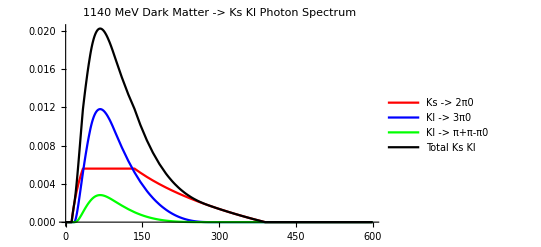

```mathematica
kshortlong[1140,600]
```

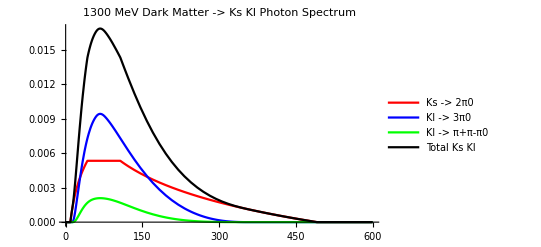

```mathematica
kshortlong[1300,600]
```

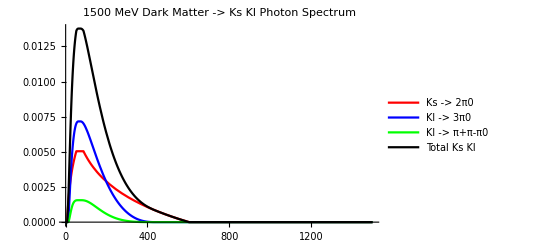

```mathematica
kshortlong[1500,1500]
```

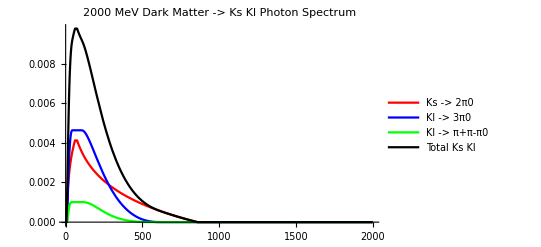

```mathematica
kshortlong[2000,2000]
```

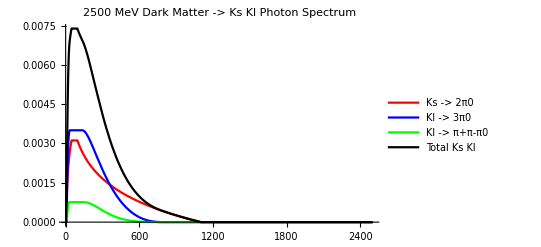

```mathematica
kshortlong[2500,2500]
```

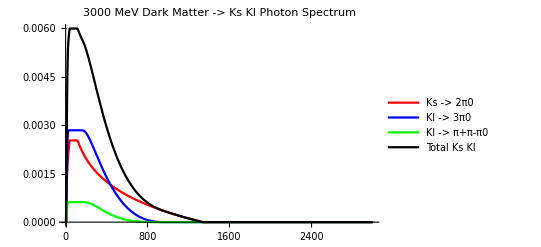

```mathematica
kshortlong[3000,3000]
```

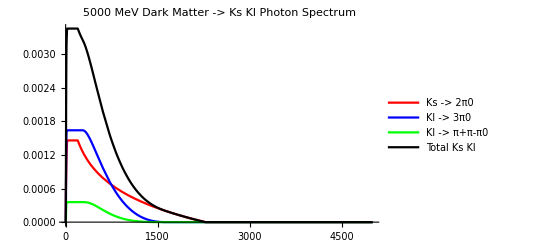

```mathematica
kshortlong[5000,5000]
```

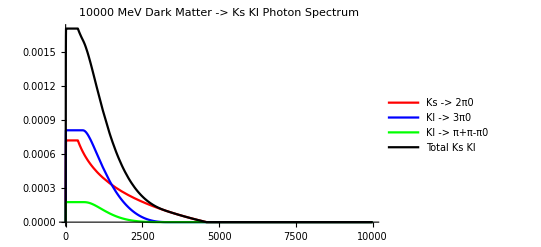

```mathematica
kshortlong[10000,10000]
```

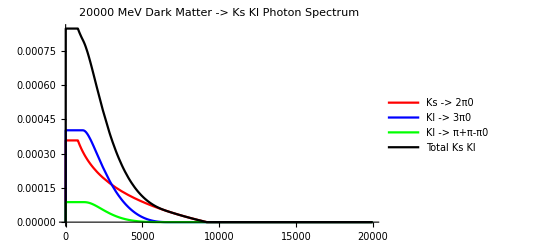

```mathematica
kshortlong[20000,20000]
```

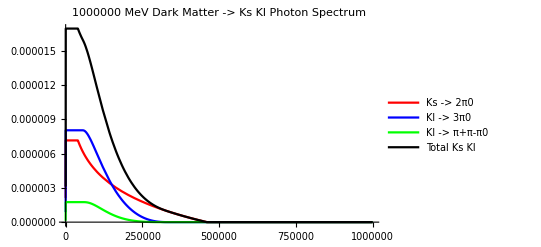

```mathematica
kshortlong[1000000,1000000]
```

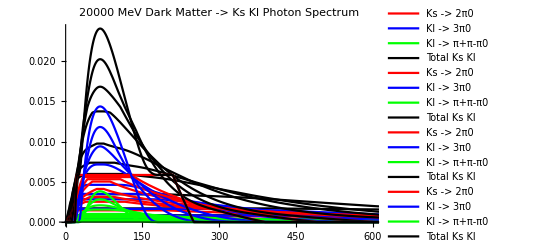

```mathematica
Show[Out[82],Out[81],Out[80],Out[79],Out[78],Out[64],Out[77],Out[76],Out[75],Out[74],PlotRange-> {{0,600},Full}]
```

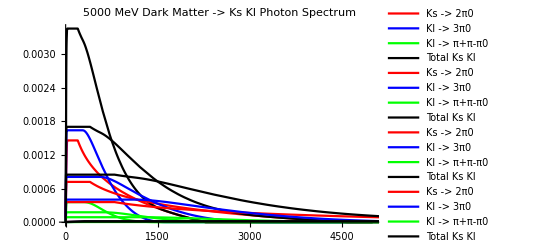

```mathematica
Show[Out[80],Out[81],Out[82],Out[98]]
```

```mathematica
justtotal[m_]:=Quiet[Plot[Evaluate[dmks2pi0norma[m,ep]+dmkl3pi0norma[m,ep]+dmklpipm0norma[m,ep]],{ep,0,m},PlotRange->Full,PlotLegends-> {m "MeV"},PlotStyle->RandomColor[]]]
```

```mathematica
totalspread[mlist_,x_]:=Show[(justtotal[#])&/@mlist,PlotRange-> {{0,x},Full}]
```

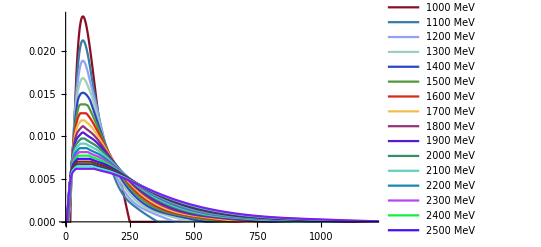

```mathematica
totalspread[Table[1000+100*(i-1),{i,20}],1200]
```

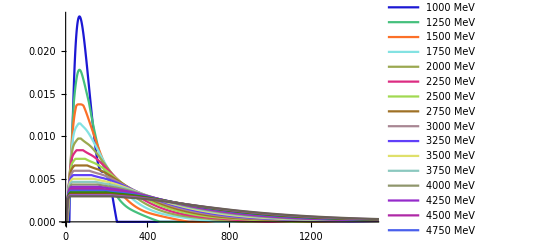

```mathematica
totalspread[Table[1000+250*(i-1),{i,20}],1500]
```

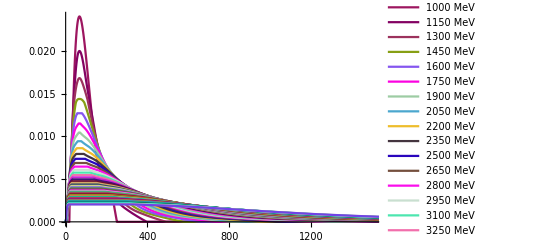

```mathematica
totalspread[Table[1000+150*(i-1),{i,50}],1500]
```

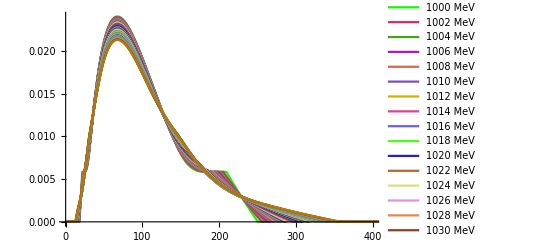

```mathematica
totalspread[Table[1000+2*(i-1),{i,50}],400]
```

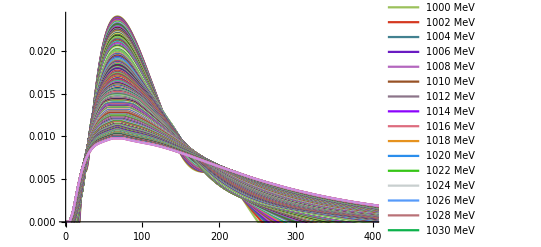

```mathematica
totalspread[Table[1000+2*(i-1),{i,500}],400]
```

```mathematica
Show[{Out[198],Out[199],Out[201],Out[207],Out[209]},PlotRange-> {{0,400},Full}]
```

-Graphics-